# “Simple model of self-supported deformed states of isolated atoms”

### Obliczenia analityczne

1) zakładamy nieskończenie ciężkie jądro atomowe: m_n ⟶ ∞, pomijamy człon p⃗ P⃗ w równianiu (6)
2) przyjęte współrzędne na płaszczyźnie (X,Y): r⃗=(r
0), p⃗=(0
p), R⃗=(R
0), P⃗=(0
P)
3) prędkość kątowa ω w kierunku Z, więc: ω⃗ x r⃗=(0
ωr
0), ω⃗ x p⃗=(-ωp
0
0), ω⃗ x R⃗=(0
ωR
0), ω⃗ x P⃗=(-ωP
0
0)
4) równania (7) na warunki stabilności układu - przyrównujemy pochodne po czasie do zera:

Piecewise[{{p/m_e=ωr, (a)}, {P/m_c=ωR
0 = -Z/r^2+(Z-1)/(R-r)^2+ωp
0 = -kR-(Z-1)/(R-r)^2+ωP, (b)

(c)

(d)}}]

### Parametry symulacji

```mathematica
me=1; (* masa elektronu rydbergowskiego*)
mc=(Z-1); (* masa chmury elektronowej *)
k=3.5; (* stała sprężystości oscylatora *)
Z=12; (* liczba atomowa, atom magnezu Mg*)
```

### Warunki stabilności układu

```mathematica
eqs={p/me==w r, pp/mc==w rr, 0==-Z/r^2+(Z-1)/(rr-r)^2+w p, 0==-k rr - (Z-1)/(rr-r)^2+w pp} (* stabilne położenia i pędy w funkcji ω *)
```

{p==r w,pp/11==rr w,0==-12/r^2+11/(-r+rr)^2+p w,0==-3.5 rr-11/(-r+rr)^2+pp w}

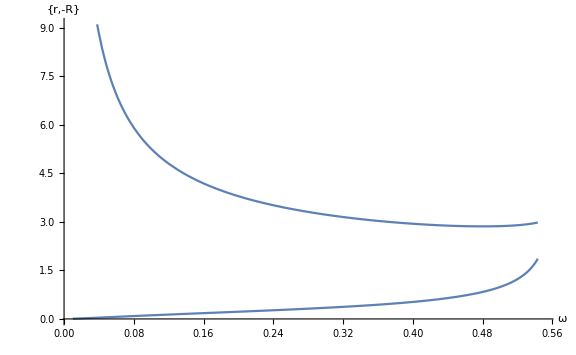

```mathematica
Plot[{r,-rr}/.(rozw=NSolve[eqs/.w-> ww,{p,pp,r,rr},Reals];rozw[[Flatten[Position[Negative[rozw[[#1,3,2]] rozw[[#1,4,2]]&@Table[i,{i,3}]],True]][[1]]]]),{ww,0.01,0.55},ImageSize->Large,AxesLabel->{"ω","{r,-R}"},BaseStyle->{Large,FontFamily->"Times",Thickness->0.003}] (* rozwiązanie układu równań i rysowanie "fizycznych" (rR<0) rozwiązań {r,-R} w funkcji częstości kołowej ω *)
```